61951.

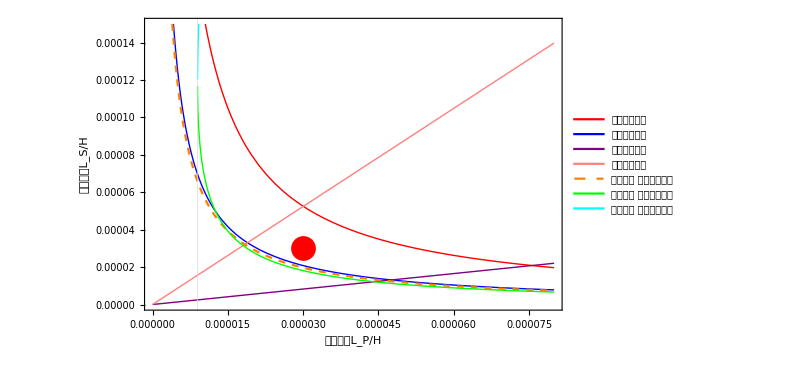

```mathematica
Dmin=0.26;
(*直流电压24V*)
V1=24;


Lp=Ls=30×10^-6;
Cp=Cs=220*10^-9;
kmin=0.1;
kmax=0.4;

Subscript[I, s1]=12;
Subscript[I, s2]=12;

(*恒流点 输出电流*)
Subscript[I, 2max]=5;

(*恒压点 输出电流*)
Subscript[I, 2min]=0.2;

(*负载电压*)
Subscript[V, 2max]=12.6;

Rla=2.4;
Rlb=6;
Rlc=8;

(*互导增益*)
kcc=Subscript[I, 2max]/V1;

(*电压增益*)
kcv=Subscript[V, 2max]/V1;

w0=1/√(Ls*Cs);
f=1/(√(Ls*Cs)*1.0*2*π)
data={Lp,Lp};

Plot[
{(64/(kmin^2*kcc^2*Lp*π^4*w0^2))*Sin[Dmin*π/2]^2,
(*电导增益*)
64/(kmax^2*kcc^2*Lp*π^4*w0^2),
kcv^2*Lp,
(*电压增益*)
kcv^2*Lp/(Sin[Dmin*π/2]^2),

8*Subscript[V, 2max]^2/(Subscript[I, s1]^2*kmin^2*Lp*π^2*w0^2),
(*恒流状态 电流增益*)

4/π^2*((Subscript[I, s1]^2*Lp*Rlb^2)/Subscript[V, 2max]^2-√((Subscript[I, s1]^4*Lp^2*Rlb^4)/Subscript[V, 2max]^4+(4*(kmin-1)*Rlb^2)/(kmin^2*w0^2))),
(*恒压状态 电流增益*)
4/π^2*((Subscript[I, s1]^2*Lp*Rlb^2)/Subscript[V, 2max]^2+√((Subscript[I, s1]^4*Lp^2*Rlb^4)/Subscript[V, 2max]^4+(4*(kmin-1)*Rlb^2)/(kmin^2*w0^2)))},
{Lp,0,80×10^-6},


GridLines->{{(2*Subscript[V, 2max]^2*√(1-kmin))/(Subscript[I, s1]^2*kmin*Rlb*w0)},{}},
GridLinesStyle->{Thick,Yellow},

PlotRange->{0,150×10^-6},
Epilog->{PointSize[0.03],Red,Point[data]},
PlotStyle->{{Red,Thick},{Blue,Thick},{Purple,Thick},{Pink,Thick},{Orange,Dashed},{Green,Thick},{Cyan,Thick}},
Frame->True,
FrameLabel->{Style["(:539f:8fb9:7535:611fL)_P/H",Black,Larger],Style["(:526f:8fb9:7535:611fL)_S/H",Black,Larger]},
PlotLegends->Placed[{"电导增益上限","电导增益下限","电压增益下限","电压增益上限","恒流状态 电流增益下限","恒压状态 电流增益下限","恒压状态 电流增益上限"},{0.65,0.75}]
]
```